# Spherically Symmetric Boson Stars

```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookDirectory[]
```

C:\Users\aleja\OneDrive\Escritorio\master\roma\new rescaling\

## Derivation of the equilibrium equations

### Metric and coordinates

Coordinates

```mathematica
x={t,r,θ,ϕ};
```

Metric  ds^2=g_tt dt^2+g_rr dr^2+g_θθ dθ^2+g_φφ dφ^2

```mathematica
gtt=-Exp[ν[r]];
grr=Exp[u[r]];
gθθ=r^2;
gϕϕ=r^2*Sin[θ]^2;
g=DiagonalMatrix[{gtt,grr,gθθ,gϕϕ}];
ginv=Inverse[g];
dim=Length[g];
```

```mathematica
g//MatrixForm
```

(-ⅇ^ν[r] | 0 | 0 | 0
0 | ⅇ^u[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Christoffel symbols and Einstein tensor

```mathematica
Γ=Table[1/2Sum[ginv[[a,d]](D[g[[d,c]],x[[b]]]+D[g[[b,d]],x[[c]]]-D[g[[b,c]],x[[d]]]),{d,1,dim}],{a,1,dim},{b,1,dim},{c,1,dim}];
Ricci=Table[Sum[D[Γ[[c,a,b]],x[[c]]]-D[Γ[[c,c,b]],x[[a]]]+Sum[Γ[[c,c,d]]Γ[[d,a,b]]-Γ[[c,a,d]]Γ[[d,c,b]],{d,1,dim}],{c,1,dim}],{a,1,dim},{b,1,dim}];
R=Sum[ginv[[a,b]]*Ricci[[a,b]],{a,1,dim},{b,1,dim}];
Einstein=Table[Ricci[[a,b]]-1/2g[[a,b]]*R,{a,1,dim},{b,1,dim}];
```

Stress - energy tensor

```mathematica
Φ[x]=Φ0[r]*Exp[ⅈ*ω*t];
T=Table[D[Φ[x],x[[a]]]**D[Φ[x],x[[b]]]+D[Φ[x],x[[a]]]*D[Φ[x],x[[b]]]*-g[[a,b]]*(Sum[ginv[[c,d]]*D[Φ[x],x[[c]]]**D[Φ[x],x[[d]]],{c,1,dim},{d,1,dim}]+V[Abs[Φ[x]]^2]),{a,1,dim},{b,1,dim}];
```

Einstein equations

```mathematica
eqn1=FullSimplify[Einstein[[1,1]]-8*Pi*T[[1,1]],{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
eqn2=FullSimplify[Einstein[[2,2]]-8*Pi*T[[2,2]],{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
```

-8 ⅇ^ν[r] π V[Φ0[r]^2]-8 π ω^2 Φ0[r]^2+(ⅇ^(-u[r]+ν[r]) (-1+ⅇ^u[r]+r (u'[r]-8 π r Φ0'[r]^2)))/r^2

8 ⅇ^u[r] π (V[Φ0[r]^2]-ⅇ^(-ν[r]) ω^2 Φ0[r]^2)+(1-ⅇ^u[r]+r ν'[r])/r^2-8 π Φ0'[r]^2

Klein - Gordon equation

```mathematica
eqn3=FullSimplify[Exp[-ⅈ*ω*t](1/Sqrt[-Det[g]]Sum[D[Sqrt[-Det[g]]ginv[[a,b]]D[Φ[x],x[[b]]],x[[a]]],{a,1,dim},{b,1,dim}]-D[V[q],q]*Φ[x])/.q->Abs[Φ[x]]^2,{Element[x,Reals],Element[{Φ0[r],Φ0'[r],ω},Reals]}]
```

Φ0[r] (ⅇ^(-ν[r]) ω^2-V'[Φ0[r]^2])+(ⅇ^(-u[r]) ((4-r u'[r]+r ν'[r]) Φ0'[r]+2 r Φ0''[r]))/(2 r)

Bosonic potentials

```mathematica
(*V[q_]:=m^2q*) (*1*)
V[q_]:=m^2q+γ q^3/3; (*2*)
(*V[q_]:=m^2q(1-2q/σ0^2)^2;*) (*3*)
```

### Coordinate rescalings

Rescaling for potential (*1*) (see https://arxiv.org/abs/1307.4812)

```mathematica
eqnn1=eqn1/. {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn1=eqnn1/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq1=FullSimplify[eqnnn1]

eqnn2=eqn2/.  {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn2=eqnn2/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq2=FullSimplify[eqnnn2]

eqnn3=eqn3/.  {Φ0[r]->Φ0[r]*m^(1/2)/γ^(1/4),Φ0'[r]->Φ0'[r]*m^2/Sqrt[γ],Φ0''[r]->m^(7/2)/γ^(3/4)*Φ0''[r],ω->m*ω,ν'[r]->m^(3/2)/γ^(1/4)*ν'[r],ν''[r]->m^(6/2)/Sqrt[γ]*ν''[r],u'[r]->m^(3/2)/γ^(1/4)*u'[r],u''[r]->m^(6/2)/Sqrt[γ]*u''[r],r->r*γ^(1/4)/m^(3/2)};
eqnnn3=eqnn3/. {Φ0[r*γ^(1/4)/m^(3/2)]->Φ0[r],Φ0'[r*γ^(1/4)/m^(3/2)]->Φ0'[r],Φ0''[r*γ^(1/4)/m^(3/2)]->Φ0''[r],ν[r*γ^(1/4)/m^(3/2)]->ν[r],ν'[r*γ^(1/4)/m^(3/2)]->ν'[r],ν''[r*γ^(1/4)/m^(3/2)]->ν''[r],u[r*γ^(1/4)/m^(3/2)]->u[r],u'[r*γ^(1/4)/m^(3/2)]->u'[r],u''[r*γ^(1/4)/m^(3/2)]->u''[r]};
eq3=FullSimplify[eqnnn3]
```

(ⅇ^(-u[r]) m^3 (ⅇ^u[r] √γ (3 ⅇ^ν[r]-8 π r^2 Φ0[r]^2 (3 ω^2+ⅇ^ν[r] (3+Φ0[r]^4)))-3 ⅇ^ν[r] (√γ (1-r u'[r])+8 m π r^2 Φ0'[r]^2)))/(3 r^2 γ)

(m^3 (8 ⅇ^(u[r]-ν[r]) π √γ Φ0[r]^2 (-3 ω^2+ⅇ^ν[r] (3+Φ0[r]^4))+(3 √γ (1-ⅇ^u[r]+r ν'[r]))/r^2-24 m π Φ0'[r]^2))/(3 γ)

(m^(5/2) (-2 ⅇ^(-ν[r]) √γ (ⅇ^ν[r]-ω^2) Φ0[r]-2 √γ Φ0[r]^5+(ⅇ^(-u[r]) m ((4-r u'[r]+r ν'[r]) Φ0'[r]+2 r Φ0''[r]))/r))/(2 γ^(3/4))

## Solving the equations

### Implementing initial conditions

Expansion in powers of r (this is done to improve initial conditions)

```mathematica
n=4;
```

```mathematica
μ[r_]:=Sum[uu[i]r^i,{i,0,2*n+2}];
v[r_]:=Sum[vv[i]r^i,{i,0,2*n+2}];
p[r_]:=Sum[pp[i]r^i,{i,0,2*n+2}];
```

```mathematica
series1=Series[eq1/.{u[r]->μ[r],u'[r]->μ'[r],u''[r]->μ''[r],ν[r]->v[r],ν'[r]->v'[r],ν''[r]->v''[r],Φ0[r]->p[r],Φ0'[r]->p'[r],Φ0''[r]->p''[r]},{r,0,2*n+4}];
series2=Series[eq2 /.{u[r]->μ[r],u'[r]->μ'[r],u''[r]->μ''[r],ν[r]->v[r],ν'[r]->v'[r],ν''[r]->v''[r],Φ0[r]->p[r],Φ0'[r]->p'[r],Φ0''[r]->p''[r]},{r,0,2*n+4}];
series3=Series[eq3 /. {u[r]->μ[r],u'[r]->μ'[r],u''[r]->μ''[r],ν[r]->v[r],ν'[r]->v'[r],ν''[r]->v''[r],Φ0[r]->p[r],Φ0'[r]->p'[r],Φ0''[r]->p''[r]},{r,0,2*n+4}];
```

```mathematica
(*Clear[uu,vv,pp]*)
```

```mathematica
uu[0]=0;
Table[pp[2i+1]=0,{i,0,n}];
Table[uu[2i+1]=0,{i,0,n}];
Table[vv[2i+1]=0,{i,0,n}];
```

```mathematica
Table[{uu[2i+2],vv[2i+2],pp[2i+2]}=Collect[Solve[{Coefficient[series1,r,2i]==0,Coefficient[series2,r,2i]==0,Coefficient[series3,r,2i]==0},{uu[2i+2],vv[2i+2],pp[2i+2]}],{vv[0],pp[0]},Simplify][[1,All,2]],{i,0,n}];
```

```mathematica
FullSimplify[μ[r]];
```

```mathematica
FullSimplify[v[r]];
```

```mathematica
FullSimplify[p[r]];
```

```mathematica
FullSimplify[p'[r]];
```

```mathematica
γ=1000;
```

```mathematica
pp[0]=1;
vv[0]=-0.3;
```

```mathematica
m=1;   (*COMPROBAR SI ESTO DEBE SER UNO*)
```

### Solution with NDSolve

```mathematica
ϵ=0.01;
```

```mathematica
prec=12;
```

```mathematica
sol1=ParametricNDSolve[{SetPrecision[eq1,prec]==0,SetPrecision[eq2,prec]==0,SetPrecision[eq3,prec]==0,u[SetPrecision[ϵ,prec]]==SetPrecision[μ[ϵ],prec],ν[SetPrecision[ϵ,prec]]==SetPrecision[v[ϵ],prec],Φ0'[SetPrecision[ϵ,prec]]==SetPrecision[p'[ϵ],prec],Φ0[SetPrecision[ϵ,prec]]==SetPrecision[p[ϵ],prec]},{Φ0,ν,u},{r,0.001,100},{ω},PrecisionGoal->8,AccuracyGoal->8,WorkingPrecision->10(*,MaxSteps->Infinity*)]
```

{Φ0→ParametricFunction[<>],ν→ParametricFunction[<>],u→ParametricFunction[<>]}

```mathematica
sol1=ParametricNDSolve[{eq1==0,eq2==0,eq3==0,u[ϵ]==μ[ϵ],ν[ϵ]==v[ϵ],Φ0'[ϵ]==p'[ϵ],Φ0[ϵ]==p[ϵ]},{Φ0,ν,u},{r,0.00001,40},{ω},PrecisionGoal->8,AccuracyGoal->8,WorkingPrecision->10(*,MaxSteps->Infinity*)]
```

{Φ0→ParametricFunction[<>],ν→ParametricFunction[<>],u→ParametricFunction[<>]}

### Frequency determination - UNA VEZ TENGO LOS VALORES BUENOS, SUSTITUIR EN wbar

```mathematica
R=0.1;
```

```mathematica
root=FindRoot[{Φ0[ω][R]/.sol1},{ω,0.9}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(ⅇ^(-u[r$251202]) (10 √10 ⅇ^u[«1»] (Times[«2»]+Times[«5»])-3 ⅇ^ν[«1»] (Times[«3»]+Times[«4»])))/(3000 r$251202^2)==0,«5»,Φ0[0.01]==1.+0.0001 (5/3 Power[«2»]+7.11438 Plus[«2»])+1.×10^-8 (125/3+«4»+«18» Plus[«1»])+«1»+1.×10^-16 ((3573200 Power[«2»])/45927+«9»+«2»)+1.×10^-20 ((53628160 Power[«2»])/649539+(4096 Power[«2»] Power[«2»])/19683+3.55047 Power[«2»]+7.41267×10^-7 Plus[«2»]+0.250826 Power[«2»] Plus[«3»]+1.25899×10^-6 Plus[«3»]+1.30689×10^-8 Plus[«3»]+5.09839×10^-6 Plus[«4»]+4.81121×10^-9 Plus[«4»]+0.0000788994 Plus[«2»] Plus[«5»]+«5»)},«3»,{}}) is less than WorkingPrecision (10.).

ParametricNDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at r == 0.1350730483.

{ω→9.06631}

```mathematica
ωbar=root[[1]][[2]]
```

9.06631

After a first iteration, ask FindRoot to search for the zero around the value of the previous iteration, i . e ., replace the initial parameter (0.9 in the example) with the value ω /. root, and gradually increase the value of R, checking each time that there are no other zeros of Φ0 between 0 and the considered value of R .

```mathematica
R=0.15;
```

```mathematica
root=FindRoot[{Φ0[ω][R]/.sol1},{ω,ωbar}]
```

ParametricNDSolve::ndsz: At r == 0.163368593, step size is effectively zero; singularity or stiff system suspected.

{ω→6.29395}

```mathematica
For[R=0.2,R<=15,R=R+0.05,root=FindRoot[{Φ0[ω][R]/.sol1},{ω,ω/.root}]];
```

ParametricNDSolve::ndsz: At r == 7.794416551, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::ndsz: At r == 6.428823163, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::ndsz: At r == 14.33570899, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve::ndsz will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {11.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NumberForm[ω/.root,15]
```

3.02191327085727

For pp[0]=1 and lamda=100, the mass is 0.1211264981, \omega=0.851197 and vv[0]=-6.71118
For pp[0]=1 and lamda=1000, the mass is 0.0699076018, \omega=0.865571 and vv[0]=-2.80042

Colors for the plots

```mathematica
{C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13}={RGBColor["#195c92"],RGBColor["#d11141"],RGBColor["#009E60"],RGBColor["#FFA500"],
RGBColor["#34DCE3"],RGBColor["#DC00E3"],RGBColor["#8FDE44"],RGBColor["#4FB6E3"],
RGBColor["#E05BE0"],RGBColor["#1370DE"],RGBColor["#B52E66"],RGBColor["#FA6705"],RGBColor["#319F8F"]};
```

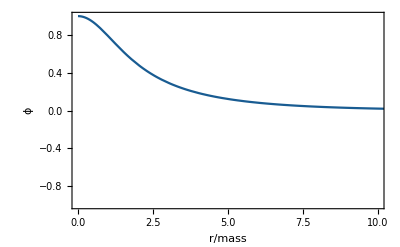

```mathematica
bsplot=Plot[Evaluate[Φ0[ω/.root][r*mass]/.sol1],{r,0,50},PlotRange->{{0,10},{-1,1}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/mass",18],Style["ϕ",18]},RotateLabel->False,PlotStyle->{Directive[C1,AbsoluteThickness[1.6]]},ImageSize->400,ImagePadding->{{80,40},{70,25}}]
```

### Time reparameterization and metric functions

```mathematica
a=Exp[ν[ω/.root][5]]/.sol1
```

14.1887463

```mathematica
ω/.root
```

3.02191

```mathematica
freq=ω/Sqrt[a-2]/.root   (*HAY QUE GUARDAR ESTO PARA LAS FRECUENCIAS, CAMBIANDO EL VALOR DE a TMB*)
```

0.865571

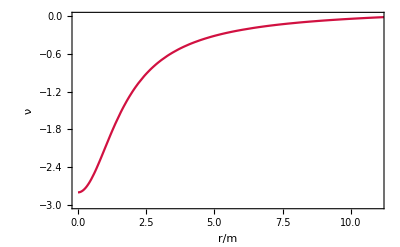

```mathematica
Plot[Evaluate[-Log[a-2]+ν[ω/.root][r*mass]/.sol1],{r,0,80},PlotRange->{{0,11},{-3,0.0}}, Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/m",18],Style["ν",18]},RotateLabel->False,PlotStyle->{Directive[C2,AbsoluteThickness[1.6]]},ImageSize->400,ImagePadding->{{80,40},{50,25}}]
```

```mathematica
Evaluate[-Log[a-2]+ν[ω/.root][0.01*mass]/.sol1]
```

-2.80042

```mathematica
+0.
```

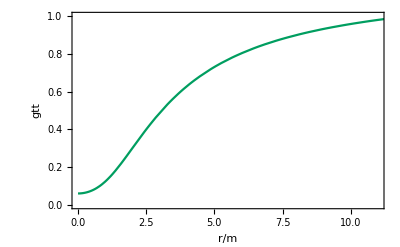

```mathematica
Plot[Evaluate[Exp[-Log[a-2]+ν[ω/.root][r*mass]/.sol1]],{r,0.001,80},PlotRange->{{0,11},{0,1}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/m",18],Style["gtt",18]},RotateLabel->False,PlotStyle->{Directive[C3,AbsoluteThickness[1.6]]},ImageSize->400,ImagePadding->{{80,40},{50,25}}]
```

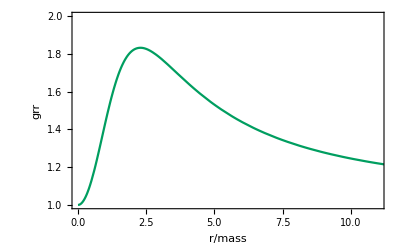

```mathematica
Plot[Evaluate[Exp[u[ω/.root][r*mass]/.sol1]],{r,0.001,80},PlotRange->{{0,11},{1,2}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/mass",18],Style["grr",18]},RotateLabel->False,PlotStyle->{Directive[C3,AbsoluteThickness[1.6]]},ImageSize->400,ImagePadding->{{80,40},{80,25}}]
```

The latter allows to derive the total mass

```mathematica
M[r_]=r/2(1-Exp[-u[ω/.root][r]/.sol1]);
```

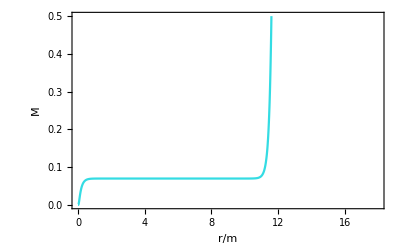

```mathematica
Plot[Evaluate[M[r]],{r,0.0001,18},PlotRange->{{0,18},{0,0.5}},Frame->True,FrameStyle->Directive[15,GrayLevel[0],FontFamily->"American Typewriter",Italic,AbsoluteThickness[1.5]],FrameLabel->{Style["r/m",18],Style["M",18]},RotateLabel->False,PlotStyle->{Directive[C5,AbsoluteThickness[1.6]]},ImageSize->400,ImagePadding->{{80,40},{50,25}}]
```

```mathematica
mass=M[10]
```

0.0699076018

### Exporting the solution

```mathematica
ϕr=Φ0[ω/.root]/.sol1
```

InterpolatingFunction[…]

```mathematica
Export["C:\\Users\\aleja\\OneDrive\\Escritorio\\master\\roma\\new rescaling\\phisol_lamda=1000_phi_1.wdx",ϕr];
```

```mathematica
gttsol=a*Exp[-ν[ω/.root]/.sol1]
```

0.8644239582 ⅇ^(-InterpolatingFunction[…])

```mathematica
Export["gttsol.wdx",gttsol];
```

```mathematica
grrsol=Exp[u[ω/.root]/.sol1]
```

ⅇ^InterpolatingFunction[…]

```mathematica
Export["grrsol.wdx",grrsol];
```